### Predict next of Graphics line with RNN

#### 1 prepare datasets

```mathematica
GT=GeometricTransformation;
ST=ScalingTransform;
TT=TranslationTransform;
RT=RotationTransform;
```

```mathematica
RandomGraphic[]:=Graphics[GT[RandomChoice[{Rectangle[#,#+RandomInteger[{1,5},2]]&@RandomInteger[{0,5},2],GT[Polygon[{{0,0},{1,1},{2,0}}],ST[RandomReal[{1.5,2.5},2]]]}],TT[RandomReal[{-5,5},2]].RT[RandomReal[{-π,π}],{0,0}]],ImageSize->256,PlotRange->{{-15,15},{-15,15}},Frame->True];
```

```mathematica
FlattenGraphics[gr_Graphics]:=Module[{gr1,gr2,gr3,gr4,gr5},gr1= Replace[gr,{Rectangle[{x1_,y1_},{x2_,y2_}]:>{Line[{{x1,y1},{x2,y1}}],Line[{{x2,y1},{x2,y2}}],Line[{{x2,y2},{x1,y2}}],Line[{{x1,y2},{x1,y1}}]},Polygon[a__]:>Line/@Partition[a,2,1,1]},All];
gr2=DeleteCases[gr1,Rotate[{{}},_,_],All];
gr3=DeleteCases[gr2,Translate[{},_],All];
gr4=Replace[List@gr3,GeometricTransformation[g__,{m__,v__}]:>Replace[g,{x_Integer|x_Real,y_Integer|y_Real}:>m.{x,y}+v,All],-1];;
gr5=Graphics[Cases[gr4,_Line,All],Options@gr]]
```

```mathematica
GraphicsTransformation2Origin[gr_]:=Module[{grF,firstLine,len,tf},firstLine=gr[[1,1,1]];
len=EuclideanDistance@@firstLine;
tf=FindGeometricTransform[{{0,0},{len,0}},firstLine][[2]];
{tf,Graphics@Replace[gr[[1]],{x_Integer|x_Real,y_Integer|y_Real}:>tf@{x,y},All]}]
```

```mathematica
GraphicsTransform2Site[gr_,tf_]:=Graphics[Replace[gr[[1]],{x_Integer|x_Real,y_Integer|y_Real}:>tf@{x,y},All],ImageSize->256,PlotRange->{{-15,15},{-15,15}},Frame->True]
```

```mathematica
Graphics2Graph[gr_Graphics]:=Module[{gr6,coords,vertices,rules,edges,graph},gr6=First@FlattenGraphics@gr;
coords=DeleteDuplicates@Cases[gr6,{x_Integer|x_Real,y_Integer|y_Real}:>1.{x,y},All];
vertices=Range@Length@coords;
rules=Thread[coords->vertices];
edges=Cases[Replace[gr6,{x_Integer|x_Real,y_Integer|y_Real}:>((1.{x,y})/.rules),All],a_Line:>DirectedEdge@@First@a,1];
graph=Graph[vertices,edges,VertexCoordinates->coords]]
```

```mathematica
Graph2Turtle[gr_Graph]:=Module[{vl,el,cl,elC,ll,al},vl=VertexList@gr;
el=List@@@EdgeList@gr;
cl=PropertyValue[gr,VertexCoordinates];
elC=Part[cl,#]&/@el;
ll=EuclideanDistance@@@elC;
al=Prepend[#[[2]]-#[[1]]&/@Partition[PlanarAngle[#[[1]]->{#[[1]]+{1,0},#[[2]]}]&/@elC,2,1],0];
Transpose[{ll,al}]]
```

```mathematica
Turtle2Graphics[tCode_]:=Module[{tPos,tAngle,tPosA},tPos={tCode[[1,1]],0};
tAngle=0;
Graphics[FoldList[(tPosA=tPos;
tAngle=tAngle+#2[[2]];
tPos=tPosA+RotationTransform[tAngle]@{#2[[1]],0};
Line[{tPosA,tPos}])&,Line[{{0,0},tPos}],Rest@tCode],Frame->True,PlotRange->10]]
```

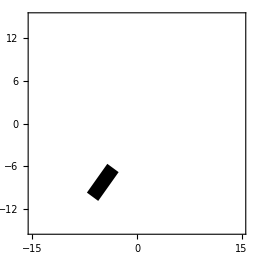

```mathematica
gr=RandomGraphic[]
```

```mathematica
Batch[n_]:=Module[{gr,tf,gr1,tur},gr=RandomGraphic[];
{tf,gr1}=GraphicsTransformation2Origin@FlattenGraphics@gr;
tur=Graph2Turtle@Graphics2Graph[gr1];
{Most@#->Last@#,tf}&@tur]&/@Range@n
```

```mathematica
dataT=Batch@100;
dataV=Batch@10;
```

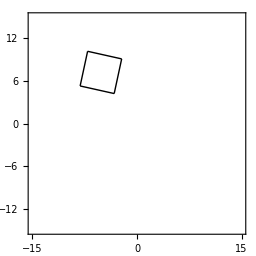

```mathematica
n=3;
que=dataV[[n,1,1]];
ans=dataV[[n,1,2]];
tf=dataV[[n,2]];
GraphicsTransform2Site[Turtle2Graphics@Append[que,ans],InverseFunction@tf]
```

```mathematica
dataV[[1]]
```

{{{2.54939,0},{2.54939,4.66205}}→{3.5135,-2.33102},TransformationFunction[(-0.615286 | 0.788304 | 5.45818
-0.788304 | -0.615286 | 1.24846
0. | 0. | 1.)]}

#### 2 setup a network

```mathematica
net=NetInitialize@NetChain[{LongShortTermMemoryLayer[12],SequenceLastLayer[],LinearLayer[2]},"Input"->{"Varying",2},"Output"->{2}]
```

NetChain[<>]

```mathematica
dataV[[1,1,1]]
```

{{2.54939,0},{2.54939,4.66205}}

```mathematica
net@dataV[[2,1,1]]
```

{-0.262352,0.107045}

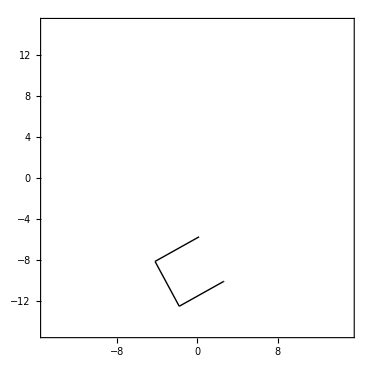

```mathematica
n=4;
que=dataV[[n,1,1]];
ans=net@dataV[[n,1,1]];
tf=dataV[[n,2]];
GraphicsTransform2Site[Turtle2Graphics@Append[que,ans],InverseFunction@tf]
```

#### 3 train and validation

```mathematica
netT=NetTrain[net,dataT[[All,1]],All,ValidationSet->dataT[[All,1]],TargetDevice->"GPU"];
```

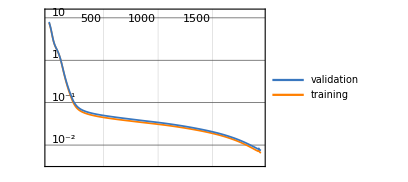
| rounds
loss | -Graphics-

<|Loss→0.00651179|>

NetChain[<>]

```mathematica
netT["LossPlot"]
netT["RoundMeasurements"]
netF=netT["TrainedNet"]
```

```mathematica
n=4;
dataV[[n,1]]
netF@dataV[[n,1,1]]
```

{{5.,0},{5.,-4.71239},{5.,1.5708}}→{5.,1.5708}

{4.99183,1.55322}

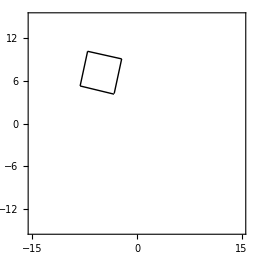

```mathematica
n=3;
que=dataV[[n,1,1]];
ans=netF@dataV[[n,1,1]];
tf=dataV[[n,2]];
GraphicsTransform2Site[Turtle2Graphics@Append[que,ans],InverseFunction@tf]
```

```mathematica
dataV[[3,1,1]]
```

{{5.,0},{5.,-4.71239},{5.,1.5708}}

```mathematica
dataV[[3,2]]
```

TransformationFunction[(0.214307 | 0.976766 | -3.42391
-0.976766 | 0.214307 | -4.09286
0. | 0. | 1.)]

### Assign class to token - sentiment

#### 1 prepare datasets

```mathematica
dataT=ExampleData[{"MachineLearning","MovieReview"},"TrainingData"];
dataV=ExampleData[{"MachineLearning","MovieReview"},"TestData"];
```

```mathematica
Length@dataV
```

3200

```mathematica
dataT[[123]]
```

fans of behan's work and of irish movies in general will be rewarded by borstal boy . →positive

#### 2 setup a network

```mathematica
net=NetInitialize@NetChain[{
EmbeddingLayer[40],
DropoutLayer[0.3],
LongShortTermMemoryLayer[20],
SequenceLastLayer[],
LinearLayer[2],
SoftmaxLayer[]},
"Input"->NetEncoder[{"Tokens"}],
"Output"->NetDecoder[{"Class",{"positive","negative"}}]]
```

NetChain[<>]

```mathematica
net["this is bad news","Probabilities"]
```

<|positive→0.503626,negative→0.496375|>

```mathematica
NetTake[net,2]@"hello world"
```

{{-0.00899579,-0.00420132,0.00931703,0.00791369,-0.00495771,-0.0109483,0.0106688,-0.00619217,-0.00142296,-0.00870255,0.00618675,-0.00974032,-0.00751939,0.0100608,0.000287109,0.00565409,0.010443,0.000912568,-0.00859314,0.000164454,0.00116419,-0.00864912,-0.00824075,-0.00586443,0.00318542,0.0105492,-0.0106205,0.00627726,0.0103059,0.00951305,-0.0102401,-0.00656964,0.00106366,-0.0052443,-0.00580744,-0.011948,-0.00464423,-0.00369445,-0.00577578,-0.00862872},{-0.00573956,-0.00915309,0.00368979,-0.0053711,0.00515217,-0.0090624,-0.0113042,0.0000339358,0.00844868,-0.0013048,0.00171047,0.00904106,0.00396619,-0.00441872,0.00433635,-0.00899174,0.011134,-0.00345577,-0.00660521,0.000236646,0.0094411,-0.00971003,0.00939349,-0.0115472,-0.0114585,0.00614227,0.00307924,-0.00623849,0.00720852,0.00292261,0.00369354,0.00780466,-0.00713399,0.00159238,0.00877218,0.00345497,0.0116698,0.0102022,0.00664418,0.0077691}}

#### 3 train and validation

```mathematica
netT=NetTrain[net,dataT,All,ValidationSet->dataV,TargetDevice->"GPU"]
```

NetTrain Results
summary | ,,  batches:2340  rounds:10  time:19s  examples/s:3991
data | ,,  training examples:7462  validation examples:3200  processed examples:74880  skipped examples:0
method | ,,  ADAMoptimizer  batch size32GPU
round | ,,  loss:3.5×10^-2  error:1.14%
validation | ,,  loss:1.27  error:26.8%
 | 
-Graphics-  training set	-Graphics-  validation set |

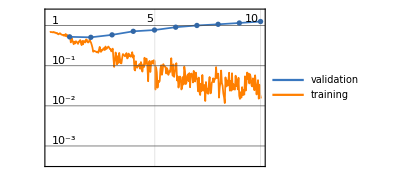
| rounds
loss | -Graphics-

<|Loss→0.0349594,ErrorRate→0.0113515|>

NetChain[<>]

```mathematica
netT["LossPlot"]
netT["RoundMeasurements"]
netF=netT["TrainedNet"]
```

```mathematica
netF@"hello world"
```

positive

```mathematica
netF["this is bad news","Probabilities"]
```

<|positive→0.184385,negative→0.815615|>

```mathematica
netF["This is not good, but I love it.", "Probabilities"]
```

<|positive→0.627057,negative→0.372943|>

### Assign class to a graphic line

#### 1 prepare datasets

```mathematica
RandomGraphic[mode_]:=Graphics[GT[Switch[mode,"Rect",Rectangle[#,#+({#,#+RandomInteger[{1,3}]}&@RandomInteger[{1,3}])]&@RandomInteger[{0,5},2],"Square",Rectangle[#,#+({#,#}&@RandomInteger[{1,5}])]&@RandomInteger[{0,5},2],"Triangle",GT[Polygon[{{0,0},{1,1},{2,0}}],ST[RandomReal[{1.5,2.5},2]]]],TT[RandomReal[{-5,5},2]].RT[RandomReal[{-π,π}],{0,0}]],ImageSize->256,PlotRange->{{-15,15},{-15,15}},Frame->True];
```

```mathematica
Batch[n_]:=Module[{mode,area,gr,tf,gr1,tur},mode=RandomChoice[{"Rect","Square","Triangle"}];
gr=RandomGraphic[mode];
area=If[Area@First@Cases[RandomGraphic[][[1,1]],_Rectangle|_Polygon,All]>5,"Large","Small"];
{tf,gr1}=GraphicsTransformation2Origin@FlattenGraphics@gr;
tur=Graph2Turtle@Graphics2Graph[gr1];
{tur->mode<>area,tf}]&/@Range@n
```

```mathematica
First@Cases[RandomGraphic[][[1,1]],_Rectangle|_Polygon,All]
Area@%
```

Rectangle[{1,0},{2,3}]

3

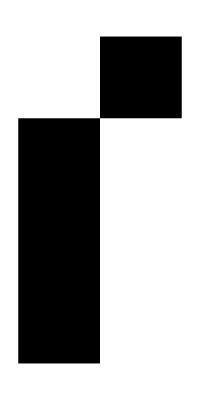

```mathematica
Graphics[{Rectangle[{2,3},{3,4}],Rectangle[{1,0},{2,3}]}]
```

```mathematica
Area@Rectangle[{1,0},{2,3}]
```

3

```mathematica
Area@Rectangle[{2,3},{3,4}]
```

Undefined

```mathematica
Batch@2
```

{{{{3.23893,0},{3.23893,4.64854},{4.43201,-2.32427}}→TriangleSmall,TransformationFunction[(-0.998992 | 0.0448913 | -0.17802
-0.0448913 | -0.998992 | 1.44396
0. | 0. | 1.)]},{{{2.49075,0},{2.49075,4.79444},{3.66395,-2.39722}}→TriangleSmall,TransformationFunction[(0.432121 | -0.901816 | -3.61958
0.901816 | 0.432121 | -1.09257
0. | 0. | 1.)]}}

```mathematica
dataT=Batch@500;
dataV=Batch@100;
```

{{1.,0},{1.,1.5708},{1.,1.5708},{1.,1.5708}}

Square<>If[Undefined,Large,Small]

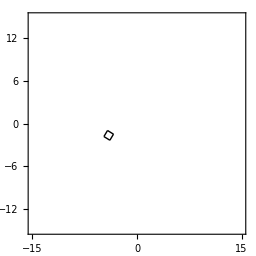

```mathematica
n=2;
que=dataV[[n,1,1]]
ans=dataV[[n,1,2]]
tf=dataV[[n,2]];
GraphicsTransform2Site[Turtle2Graphics@que,InverseFunction@tf]
```

#### 2 setup a network

```mathematica
net=NetInitialize@NetChain[{LongShortTermMemoryLayer[12],SequenceLastLayer[],LinearLayer[6],SoftmaxLayer[]},"Input"->{"Varying",2},"Output"->NetDecoder[{"Class",{"RectSmall","SquareSmall","TriangleSmall","RectLarge","SquareLarge","TriangleLarge"}}]]
```

```mathematica
n=2;
dataV[[n,1]]
```

{{3.08004,0},{3.08004,4.49529},{3.85829,-2.24764}}→TriangleSmall

```mathematica
net[dataV[[n,1,1]],"Probabilities"]
```

NetChain::invindata3: Data supplied to port "Input" could not be encoded; input was not a string.

$Failed

#### 3 train and validation

```mathematica
netT=NetTrain[net,dataT[[All,1]],All,ValidationSet->dataT[[All,1]],TargetDevice->"GPU"];
```

NetTrain::encgenfail1: Could not encode input number 1 for port "Input": input was not a string. Please check the example.

```mathematica
netT["LossPlot"]
netT["RoundMeasurements"]
netF=netT["TrainedNet"]
```

```mathematica
n=2;
dataV[[n,1]]
```

```mathematica
netF[dataV[[n,1,1]],"Probabilities"]
```

```mathematica
n=9;
que=dataV[[n,1,1]]
ans=dataV[[n,1,2]]
pre=netF@dataV[[n,1,1]]
tf=dataV[[n,2]];
GraphicsTransform2Site[Turtle2Graphics@que,InverseFunction@tf]
```

```mathematica
ClassifierMeasurements[netF,dataV[[All,1]],"WorstClassifiedExamples"]
```

### Identify multiple objects in fixed positions

#### 1 prepare datasets

```mathematica
Batch[n_]:=Module[{vec,img},vec=RandomChoice[{20,1,1}->{0,1,2},{6,6}];
img=ColorConvert[Rasterize[Graphics[Module[{d=.3},{{LightGray,Rectangle[{.5,.5},{6.5,6.5}]},Black,Thickness@Scaled@.02,MapIndexed[Replace[#1,{0:>{},1:>{Line[{#2+{-d,0},#2+{d,0}}],Line[{#2+{0,-d},#2+{0,d}}]},2:>Rectangle[#2-{d,d},#2+{d,d}]},All]&,vec,{2}]}],Frame->False,ImageSize->128],RasterSize->32],"Grayscale"];
(img->Flatten@vec)]&/@Range@n
```

```mathematica
Batch@4
```

{-Graphics-→{0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0},-Graphics-→{1,0,0,0,0,0,0,0,0,0,0,1,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},-Graphics-→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,2,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0},-Graphics-→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,0}}

```mathematica
dataT=Batch@100;
dataV=Batch@10;
```

#### 2 setup a network

which is similar to YOLO.

```mathematica
net=NetInitialize@NetChain[{
ConvolutionLayer[20,5],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
ConvolutionLayer[20,5],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
FlattenLayer[],
Tanh,
LinearLayer[120],
ElementwiseLayer[Ramp],
LinearLayer[36]},
"Input"->NetEncoder[{"Image",{32,32},"Grayscale"}],
"Output"->{36}]
```

NetChain[<>]

#### 3 train and validation

```mathematica
netT=NetTrain[net,dataT,All,ValidationSet->dataV,TargetDevice->"GPU"];
```

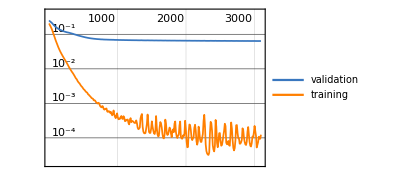
| rounds
loss | -Graphics-

<|Loss→0.000141903|>

NetChain[<>]

```mathematica
netT["LossPlot"]
netT["RoundMeasurements"]
netF=netT["TrainedNet"]
```

```mathematica
netT["LossPlot"]
netT["RoundMeasurements"]
netF=netT["TrainedNet"]
```

| rounds
loss | -Graphics-

<|Loss→0.000141903|>

NetChain[<>]

```mathematica
n=2;
dataV[[n,1]]
netF@%;
dataV[[n,2]]
Round[%]
```

-Graphics-

{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,2,0,0,0,0,0,0,2,0,0,0,0,0}

{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,2,0,0,0,0,0,0,2,0,0,0,0,0}

### Incremental interactive training - class 2 class

#### 1 setup a network

```mathematica
classesIn={"a","b","c"};
classesOut={"A","B","C"};
```

```mathematica
netT=NetInitialize@NetChain[{LinearLayer[3],SoftmaxLayer[]},"Input"->NetEncoder[{"Class",classesIn}],"Output"->NetDecoder[{"Class",classesOut}]]
```

NetChain[<>]

#### 2 create new samples

```mathematica
AddTrainingData[]:=Module[{in,out,rulesIn,rulesOut,res},in=RandomChoice[classesIn];
out=netT@in;
rulesIn=Thread[classesOut->Range@Length@classesOut];
rulesOut=Thread[Range@Length@classesOut->classesOut];
res=FormFunction[FormObject[<|" "-><|"Interpreter"->rulesIn,"Control"->RadioButtonBar,"Default"->out|>|>,AppearanceRules-><|
"Title"->"evaluate the prediction","Description"->Text[Row[{"the predicted value of ",Style[in,Red,24]," is ",Style[out,Red,24],".\nCorrect it if it is wrong:"}]]|>]][][" "]/.rulesOut;
If[Head@res===String,trainingData=Append[trainingData,in->res]]]
```

```mathematica
trainingData={};
```

```mathematica
AddTrainingData[]
```

{c→C,b→B,b→B,a→A,a→A,a→A,b→A,b→B,a→A,a→A,b→B,b→B,a→A,b→B,c→C,c→C,c→C,c→A,c→C,c→C,b→B,c→C,b→B,a→A,c→C,c→C,b→B,b→B,b→B,a→A,b→B,b→B,c→C,b→B,a→A,b→B,b→B,b→B,a→A,c→C,c→C}

#### 3 retrain the network

```mathematica
netT= NetTrain[netT, trainingData,TargetDevice->"GPU"]
```

NetChain[<>]

### Incremental interactive training - image 2 class

#### 1 setup a network

```mathematica
classesShape={"Rect","Disk","Circle","Triangle"};
classesColor={Red,Green,Blue};
```

```mathematica
netConv=NetChain[{ConvolutionLayer[4,4],Ramp,PoolingLayer[2,2],ConvolutionLayer[4,4],Ramp,PoolingLayer[2,2],FlattenLayer[]},"Input"->NetEncoder[{"Image",{32,32},"RGB"}]]
```

NetChain[<>]

```mathematica
netT=NetInitialize@NetGraph[{netConv,LinearLayer[4],SoftmaxLayer[],LinearLayer[3],SoftmaxLayer[]},{NetPort["Input"]->1->2->3->NetPort["shape"],1->4->5->NetPort["color"]},"shape"->NetDecoder[{"Class",classesShape}],"color"->NetDecoder[{"Class",classesColor}]]
```

NetGraph[<>]

#### 2 create new samples

```mathematica
GenerateRandomInput[]:=Rasterize[Graphics[{RandomChoice@classesColor,RandomChoice@{Rectangle[{-.5,-.5},{.5,.5}],Disk[{0,0},.5],{Disk[{0,0},.5],White,Disk[{0,0},.4]},Triangle[{{-.5,-.5},{0,.5},{.5,-.5}}]}},PlotRange->1,ImageSize->64],RasterSize->64]
```

```mathematica
GenerateRandomInput[]
netT@%
```

-Graphics-

<|color→RGBColor[0, 0, 1],shape→Rect|>

```mathematica
AddTrainingData[]:=Module[{in,out,rulesIn,rulesOut,res},in=GenerateRandomInput[];
out=netT@in;
rulesIn=Thread[classesOut->Range@Length@classesOut];
rulesOut=Thread[Range@Length@classesOut->classesOut];
res=FormFunction[FormObject[<|"shape"-><|"Interpreter"->classesShape,"Control"->RadioButtonBar,"Default"->out@"shape"|>,"color"-><|"Interpreter"->classesColor,"Control"->RadioButtonBar,"Default"->out@"color"|>|>,AppearanceRules-><|"Title"->"evaluate the prediction","Description"->Text[Row[{"the predicted values of image \n",in,"\nare: ",Style[out@"shape",Bold,16],"  with color ",out@"color",".\n\nCorrect them if they are wrong:"}]]|>]][];;
If[Head@res===Association,trainingData=Append[trainingData,Prepend[res,"Input"->in]]]]
```

```mathematica
trainingData={};
```

```mathematica
AddTrainingData[]
```

{<|Input→-Graphics-,shape→Circle,color→RGBColor[1, 0, 0]|>,<|Input→-Graphics-,shape→Circle,color→RGBColor[1, 0, 0]|>,<|Input→-Graphics-,shape→Triangle,color→RGBColor[0, 0, 1]|>,<|Input→-Graphics-,shape→Circle,color→RGBColor[0, 0, 1]|>,<|Input→-Graphics-,shape→Disk,color→RGBColor[1, 0, 0]|>,<|Input→-Graphics-,shape→Circle,color→RGBColor[1, 0, 0]|>,<|Input→-Graphics-,shape→Triangle,color→RGBColor[0, 0, 1]|>,<|Input→-Graphics-,shape→Disk,color→RGBColor[0, 0, 1]|>,<|Input→-Graphics-,shape→Disk,color→RGBColor[1, 0, 0]|>,<|Input→-Graphics-,shape→Triangle,color→RGBColor[0, 1, 0]|>,<|Input→-Graphics-,shape→Triangle,color→RGBColor[1, 0, 0]|>,<|Input→-Graphics-,shape→Disk,color→RGBColor[0, 0, 1]|>,<|Input→-Graphics-,shape→Circle,color→RGBColor[1, 0, 0]|>,<|Input→-Graphics-,shape→Disk,color→RGBColor[0, 1, 0]|>,<|Input→-Graphics-,shape→Triangle,color→RGBColor[0, 0, 1]|>,<|Input→-Graphics-,shape→Triangle,color→RGBColor[0, 0, 1]|>,<|Input→-Graphics-,shape→Rect,color→RGBColor[0, 1, 0]|>,<|Input→-Graphics-,shape→Triangle,color→RGBColor[0, 0, 1]|>,<|Input→-Graphics-,shape→Rect,color→RGBColor[1, 0, 0]|>,<|Input→-Graphics-,shape→Circle,color→RGBColor[0, 1, 0]|>,<|Input→-Graphics-,shape→Rect,color→RGBColor[1, 0, 0]|>,<|Input→-Graphics-,shape→Disk,color→RGBColor[1, 0, 0]|>,<|Input→-Graphics-,shape→Rect,color→RGBColor[1, 0, 0]|>,<|Input→-Graphics-,shape→Disk,color→RGBColor[0, 1, 0]|>,<|Input→-Graphics-,shape→Disk,color→RGBColor[1, 0, 0]|>,<|Input→-Graphics-,shape→Triangle,color→RGBColor[1, 0, 0]|>,<|Input→-Graphics-,shape→Circle,color→RGBColor[0, 1, 0]|>,<|Input→-Graphics-,shape→Triangle,color→RGBColor[0, 1, 0]|>,<|Input→-Graphics-,shape→Circle,color→RGBColor[1, 0, 0]|>,<|Input→-Graphics-,shape→Circle,color→RGBColor[0, 0, 1]|>,<|Input→-Graphics-,shape→Disk,color→RGBColor[1, 0, 0]|>,<|Input→-Graphics-,shape→Triangle,color→RGBColor[1, 0, 0]|>,<|Input→-Graphics-,shape→Disk,color→RGBColor[0, 0, 1]|>,<|Input→-Graphics-,shape→Circle,color→RGBColor[0, 1, 0]|>,<|Input→-Graphics-,shape→Triangle,color→RGBColor[1, 0, 0]|>,<|Input→-Graphics-,shape→Disk,color→RGBColor[0, 1, 0]|>,<|Input→-Graphics-,shape→Disk,color→RGBColor[0, 1, 0]|>,<|Input→-Graphics-,shape→Disk,color→RGBColor[1, 0, 0]|>,<|Input→-Graphics-,shape→Rect,color→RGBColor[0, 1, 0]|>,<|Input→-Graphics-,shape→Triangle,color→RGBColor[0, 0, 1]|>}

#### 3 retrain the network

```mathematica
netT = NetTrain[netT,trainingData,TargetDevice->"GPU"]
```

NetGraph[<>]